## Лаб. работа 5 Крюк В.В. 221703 Вариант 4

### Задание 1

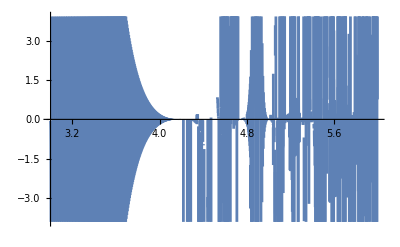

```mathematica
f[x_]:= Cot[Sinh[2x-1]]^3;
Subscript[x, 0]=9.04;
initialPlot=Plot[f[x],{x, 3,6}];
Show[initialPlot]
```

### a) функ. D

```mathematica
Print["Производная 1-го порядка: ", d1=D[f[x],x]/.x->Subscript[x, 0]]
Print["Производная 2-го порядка: ", d2=D[f[x],{x,2}]/.x->Subscript[x, 0] ]
```

Производная 1-го порядка: -9.21155×10^7

Производная 2-го порядка: 1.38172×10^16

### б)формулы числ. дифференцирования

```mathematica
FiniteDifference1[y_,y1_]:=y1-y; (* Функции конечных разностей 3-х порядков*)
FiniteDifference2[y_,y1_,y2_]:=y2-2y1+y;
FiniteDifference3[y_,y1_,y2_,y3_]:=y3-3y2+3y1-y;
h=0.1;
y1=1/h(FiniteDifference1[f[Subscript[x, 0]],f[Subscript[x, 0]+h]]-1/2*FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]+1/3*FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
y2=1/h^2(FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]-FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
```

```mathematica
Print["Производная 1-го порядка: ", y1]
Print["Производная 2-го порядка: ", y2]

Print["Разница между вычисленными значениями 1-й производной: ",Abs[d1-y1]]
Print["Разница между вычисленными значениями 2-й производной: ",Abs[d2-y2]]
```

Производная 1-го порядка: -16242.2

Производная 2-го порядка: 270672.

Разница между вычисленными значениями 1-й производной: 9.20992×10^7

Разница между вычисленными значениями 2-й производной: 1.38172×10^16

```mathematica
h=0.01;
```

```mathematica
y1=1/h(FiniteDifference1[f[Subscript[x, 0]],f[Subscript[x, 0]+h]]-1/2*FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]+1/3*FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
y2=1/h^2(FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]-FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
```

```mathematica
Print["Производная 1-го порядка: ", y1]
Print["Производная 2-го порядка: ", y2]

Print["Разница между вычисленными значениями 1-й производной: ",Abs[d1-y1]]
Print["Разница между вычисленными значениями 2-й производной: ",Abs[d2-y2]]
```

Производная 1-го порядка: 4881.37

Производная 2-го порядка: -816148.

Разница между вычисленными значениями 1-й производной: 9.21203×10^7

Разница между вычисленными значениями 2-й производной: 1.38172×10^16

### Задание 2

### а)

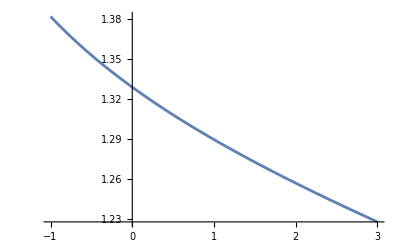

```mathematica
f[x_]:= Sinh[2+Cot[(x+3)^(1/3)]]^(1/5)
Plot[f[x], {x,-1,3}]
```

```mathematica
a=-1;
b=3;
h=0.2;
data=Table[{x,(f[x+h]-f[x-h])/(2h)},{x,a,b,h}];
TableForm[data,TableHeadings->{None,{"x_i","y'_i"}}]
```

x_i | y'_i
-1. | -0.0655454
-0.8 | -0.0595515
-0.6 | -0.0547112
-0.4 | -0.0507329
-0.2 | -0.0474151
0. | -0.0446141
0.2 | -0.0422249
0.4 | -0.040169
0.6 | -0.0383868
0.8 | -0.036832
1. | -0.0354684
1.2 | -0.0342669
1.4 | -0.0332045
1.6 | -0.0322621
1.8 | -0.0314242
2. | -0.0306781
2.2 | -0.0300131
2.4 | -0.02942
2.6 | -0.0288914
2.8 | -0.0284208
3. | -0.0280027

### б)

```mathematica
Derivate=D[f[x],x]
```

-(Cosh[2+Cot[(3+x)^(1/3)]] Csc[(3+x)^(1/3)]^2)/(15 (3+x)^(2/3) Sinh[2+Cot[(3+x)^(1/3)]]^(4/5))

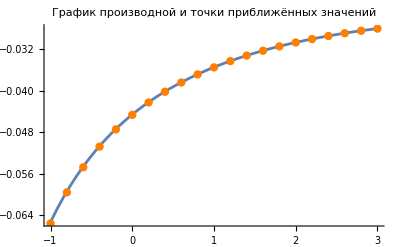

```mathematica
graph=Plot[Derivate,{x,-1,3}];
points=ListPlot[data,PlotStyle->{PointSize[0.015],Orange}];
Show[graph,points, PlotLabel-> "График производной и точки приближённых значений"]
```

### Задание 3

### а) формула средних прямоугольников

```mathematica
f[x_]:= (x+2×(x^2+0.8)^(1/5))/(0.2 x^2+√(3x+1))
a=3;
b=4.2;
Subscript[x, 0]=a;
n1=8;
step=(b-a)/n1;
For[i=1,i<=n1,i++, Subscript[x, i]=step+Subscript[x, i-1];]
AverageRectangle1=(b-a)/n1*∑_(i=1)^n1 f[Subscript[x, i-1]+(b-a)/(2*n1)]
```

1.39017

```mathematica
n2=10;
step=(b-a)/n2;
For[i=1,i<=n2,i++, Subscript[x, i]=step+Subscript[x, i-1];]
AverageRectangle2=(b-a)/n2*∑_(i=1)^n2 f[Subscript[x, i-1]+(b-a)/(2*n2)]
```

1.39018

#### Уточнение по Ричардсону

```mathematica
k=2;
Richardson=AverageRectangle2+n1^k/(n2^k-n1^k)(AverageRectangle2-AverageRectangle1)
```

1.39018

### б)Метод трапеций

```mathematica
n1=8;
Subscript[x, 0]=a;
step=(b-a)/n1;
For[i=1,i<=n1,i++, Subscript[x, i]=step+Subscript[x, i-1];]
Trapezoidal1=(b-a)/n1*(∑_(i=1)^(n1-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n1]]/2)
```

1.3902

```mathematica
n2=10;
Subscript[x, 0]=a;
step=(b-a)/n2;
For[i=1,i<=n2,i++,
Subscript[x, i]=step+Subscript[x, i-1];]
Trapezoidal2=(b-a)/n2*(∑_(i=1)^(n2-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n2]]/2)
```

1.3902

#### Уточнение по Ричардсону

```mathematica
Richardson=Trapezoidal2+n1^k/(n2^k-n1^k)(Trapezoidal2-Trapezoidal1)
```

1.39018

### Задание 4

#### Разбиение отрезка интегрирования на 8 частей

```mathematica
data=({{0.3, -1.1052}, {0.396, -1.1225}, {0.492, -1.0678}, {0.588, -0.9554}, {0.684, -0.7949}, {0.78, -0.5930}, {0.876, -0.3548}, {0.972, -0.0844}, {1.068, 0.2150}});
```

```mathematica
a=0.3;
b=1.068;
n=4;
h=(b-a)/(2n)
```

0.096

```mathematica
For[i=0,i<=2*n,i++, Subscript[y, i]=data[[i+1,2]];]
```

```mathematica
Simpsons=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

-0.523085

#### Разбиение отрезка интегрирования на 16 частей

```mathematica
data=({{0.3, -1.1052}, {0.348, -1.0799}, {0.396, -1.1225}, {0.444, -1.0598}, {0.492, -1.0678}, {0.54, -0.9782}, {0.588, -0.9554}, {0.636, -0.8462}, {0.684, -0.7949}, {0.732, -0.6713}, {0.78, -0.5930}, {0.828, -0.4594}, {0.876, -0.3548}, {0.924, -0.2147}, {0.972, -0.0844}, {1.02, 0.0593}, {1.068, 0.2150}});
```

```mathematica
n=8;
h=(b-a)/(2n)
For[i=0,i<=2*n,i++, Subscript[y, i]=data[[i+1,2]];]
```

0.048

```mathematica
Simpsons=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

-0.509386

### Задание 5

#### Формула Гаусса (4 узла)

```mathematica
f[x_]:= (ⅇ^(-x^2+5x))/(3x+0.8);
a=1.4;
b=2.9;
n=4;
polynomial = LegendreP[n,x]
```

1/8 (3-30 x^2+35 x^4)

```mathematica
soluton=NSolve[polynomial==0,x];
xx=x/.soluton
```

{-0.861136,-0.339981,0.339981,0.861136}

```mathematica
T=Table[If[i==1,1,(xx[[j]])^(i-1)],{i,n},{j,n}];MatrixForm[T]
```

(1 | 1 | 1 | 1
-0.861136 | -0.339981 | 0.339981 | 0.861136
0.741556 | 0.115587 | 0.115587 | 0.741556
-0.638581 | -0.0392974 | 0.0392974 | 0.638581)

```mathematica
B=Table[If[EvenQ[i]==True,0,2/i],{i,n}]//N
```

{2.,0.,0.666667,0.}

```mathematica
A=LinearSolve[T,B]
```

{0.347855,0.652145,0.652145,0.347855}

```mathematica
Integral=(b-a)/2*∑_(i=1)^n A[[i]]*f[(b+a)/2+(b-a)/2*xx[[i]]]
```

81.3349